```mathematica
(* 
   UnderBar[Altera o tamanho da fonte (permanentemente):]

  >> Format -> Option Inspector 
         -> Em 'Show option values': mude de 'Selection' para 'Global Preferences'
        -> Notebook Options 
       -> Display Options 
      -> Em 'Magnification' mude de 1.0 para 1.25  

Referência: https://mathematica.stackexchange.com/questions/1310/how-to-set-default-magnification-for-all-windows
*)
```

# DG Package

## 1) Instance Creation and Plot Routines

Instance Creation: DG
DGAllEdges, DGEdgeWeight, DGEdgeDistanceBounds, DGProblem, DGSaveProblem, DGGraphGetIJD

## Source Code

```mathematica
ClearAll[
DGAllEdges,
DGEdgeWeight,
DGEdgeDistanceBounds,
DGProblem,
DGPrintGraph,
DGPrintX,
DGSaveProblem,
DGGraphGetIJD
  ];

DGAllEdges[n_] := Module[{i, j, k = 0, pij},
   pij = Table[0, {i, (n (n - 1))/2}];
   For[i = 1, i <= n, i++,
    For[j = (i + 1), j <= n, j++,
      k++;
      pij[[k]] = i <-> j;
      ];
    ];
   Return[pij]
   ];

DGEdgeWeight[G_, E_] :=
  (* Gets edge weight. 'E' can be a single edge or a list of edges; *)
  Module[
{i, eij,wij, D = {}},
If[Not[FailureQ[PropertyValue[{G, E[[1]]}, EdgeWeight]]],
(* E is a list of edges *)
For[i = 1, i <= Length[E], i++,
eij = E[[i]];
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[wij=PropertyValue[{G, eij}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]];
AppendTo[D, wij]],
(* E is a single edge *)
eij = E;
If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
If[FailureQ[D = PropertyValue[{G, E}, EdgeWeight]],Throw[{"InvalidEdge:",eij}]]
];
Return[D]
];

DGEdgeDistanceBounds[G_, E_] := Module[
   {eij = E, Lij, Uij, Vij},
   If[eij[[1]] > eij[[2]], eij = eij[[2]] <-> eij[[1]]];
   Vij = PropertyValue[{G, eij}, "DistanceBounds"];
   Return[Vij]
   ];

DGProblem[x_,eij_: {},dijEps_: {}] :=
  (* Creates a problem P such that P["G"] is the problem graph and P["X"] is a problem solution; *)
  Module[{i,j,d,dij,k,numberOfAtoms,G,E,DijEps},
   (* set default values *)
   If[Length[eij]>0,E=eij,E=DGAllEdges[Length[x]]];
   If[Length[dijEps]>0,DijEps=dijEps,DijEps=Table[0,{i,Length[E]}]];
   (* unpacks the edges and calculate distances *)
   i=Table[E[[k]][[1]],{k,Length[E]}];
   j=Table[E[[k]][[2]],{k,Length[E]}];
   d=Table[N[Norm[x[[i[[k]]]] - x[[j[[k]]]]]], {k, Length[E]}];
   numberOfAtoms = Max[i, j];
   (* creates distance matrix *)
   G=Table[Infinity, {i, 1, numberOfAtoms}, {j, 1, numberOfAtoms}];
   For[k=1,k≤Length[i],k++,
      G[[i[[k]]]][[j[[k]]]]=d[[k]];
      G[[j[[k]]]][[i[[k]]]]=d[[k]]
    ];
   (* creates the graph *)
   G = WeightedAdjacencyGraph[G];
   (* adds distance bounds *)
   If[Length[DijEps]!=Length[i],Throw["InvalidInput: eij and dijEps must have the same size"]]; 
   For[k=1,k≤Length[i],k++,
    dij=DGEdgeWeight[G,i[[k]]<->j[[k]]];
    PropertyValue[{G,i[[k]]<->j[[k]]},"DistanceBounds"]={(1-DijEps[[k]]),(1+DijEps[[k]])}*dij
    ];
   Return[<|"X"->x,"G"->G|>]
   ];

DGPrintGraph[G_]:=Module[{edges,table,eij,i,j,k,Lij,Uij,Dij},
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,5}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=DGEdgeDistanceBounds[G,eij];
Dij=DGEdgeWeight[G,eij];
table[[k]]={i,j,Dij,Lij,Uij}
];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]];
Return[TableForm[table,TableHeadings->{Table[i,{i,Length[edges]}],{"i","j","dij","lij","uij"}}]]
];

DGPrintX[X_]:=Print[TableForm[X, TableHeadings -> {Table[i, {i, Length[X]}], {"x", "y", "z"}}]]; 

DGPrintDistanceMatrix[X_,edges_]:=Module[{E=edges,table,i,j,k},
table=Table[{i=E[[k]][[1]],j=E[[k]][[2]],N[Norm[X[[i]]-X[[j]]]]},{k,Length[E]}];
Print[TableForm[table,TableHeadings->{Table[i,{i,Length[E]}], {"i","j","dij"}}]]
];
DGPrintDistanceMatrix[X_]:=Module[{edges},
edges=DGAllEdges[Length[X]];
DGPrintDistanceMatrix[X,edges]
];

DGSaveProblem[P_, fname_] :=
  (* Create the files fname.csv and fname_xsol.csv with, respectively, the DG constraints given by P["G"] and one associated solution P["X"] *)
  Module[{edges, fid, table, eij, i, j, k, X, G, Dij, Lij, Uij},
   (* creates and saves solution table *)
   table = Table[P["X"][[i]][[j]], {i, Length[P["X"]]}, {j, 3}];
   fid = StringJoin[fname, "_xsol.csv"];
   Print["Saving solution file ", fid];
   Export[fid, table, TableHeadings -> {"x", "y", "z"}];
   (* creates and saves constraints table *)
   G = P["G"];
   edges = EdgeList[G];
   table = Table[0, {i, Length[edges]}, {j, 5}];
   For[k = 1, k <= Length[edges], k++,
    eij = edges[[k]];
    {i, j} = {eij[[1]], eij[[2]]};
    {Lij, Uij} = DGEdgeDistanceBounds[G, eij];
    Dij = DGEdgeWeight[G, eij];
    table[[k]] = {i, j, N[Dij], N[Lij], N[Uij]}
    ];
   fid = StringJoin[fname, ".csv"];
   Print["Saving constraints file ", fid];
   Export[fid, table, TableHeadings -> {"I", "J", "D", "L", "U"}];
   ];

DGGraphGetIJD[G_]:=Module[{i,j,k,d,E},
E=EdgeList[G];
i=Table[E[[k]][[1]],{k,Length[E]}];
j=Table[E[[k]][[2]],{k,Length[E]}];
d=Table[DGEdgeWeight[G,E[[k]]],{k,Length[E]}];
Return[{i,j,d}];
]
```

Instance Creation: MDGP
DGSetXByCartesianSystem, DGSetXByHomogeneousCoords, DGRandom3DBackbone, DGRandomMDGP, DGCalculateProteinAngles, DGCalculateProteinAnglesForAtomAtPosition, DGCalculateTorsionAngles

## Source Code

```mathematica
ClearAll[
DGSetXByCartesianSystem,
DGSetXByHomogeneousCoords,
DGRandom3DBackbone,
DGRandomMDGP,
DGPlaneAndTorsionAngles
];
DGSetXByCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];

DGSetXByHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];

DGRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=DGSetXByHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=DGSetXByCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];

DGEdgesMDGP[numberOfAtoms_]:=Module[{i,j,edges={}},
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤Min[i+3,numberOfAtoms],j++,
AppendTo[edges,i<->j];
];
];
Return[edges]
];

DGRandomMDGP[numberOfAtoms_,dijEps_:0.0,dijMax_:Infinity,seed_:0]:=
(* Generates a random MDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijEps: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijEps) and uij = (1+dijEps); 
   dijMax: all distances greater than dijMax are dropped;
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,X,D,E,dij,DijEps},
X=DGRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed]["Points"];
E={};
DijEps={};
(* set distance bounds *)
For[i=1,i≤numberOfAtoms,i++,
For[j=i+1,j≤numberOfAtoms,j++,
(* exact distances *)
If[Abs[i-j]≤2,
AppendTo[E,{i,j}];
AppendTo[DijEps,0];
Continue[];
];
(* intervalar distances *)
If[Abs[i-j]==3||N[Norm[X[[i]]-X[[j]]]]<dijMax,
AppendTo[E,{i,j}];
AppendTo[DijEps,dijEps]
];
];
];
Return[DGProblem[X,E,DijEps]]
];

DGPlaneAndTorsionAngles[A_,B_,C_,D_,verbose_:False]:=
(* Calculates the plane and torsion for 3D points A, B, C and D in that order. *)
Module[
{nabc, nbcd,θ,ω},
(* centered at C *)
θ=VectorAngle[B-C,D-C];
If[verbose,Print["(θ):Angle[BCD]  =",θ]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
ω=VectorAngle[nabc,nbcd];
If[verbose,Print["(ω):Angle[ABCD] =",ω]];
Return[{θ,ω}];
];

DGPlaneAndTorsionAngles[X_,i_]:=
(* Calculates plane and torsion angles of i-th atom. *)
DGPlaneAndTorsionAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];

DGPlaneAndTorsionAngles[X_]:=Module[
{θ,ω,i},
ω=Table[0,{i,Length[X]}];
θ=Table[0,{i,Length[X]}];
For[i=4,i≤Length[X],i++,
{θ[[i]],ω[[i]]}=DGPlaneAndTorsionAngles[X,i]
];
Return[{θ,ω}]
];
```

Plot Routines
DGPlot3DBackbone, DGPlotAdjacencyMatrix

## Source Code

```mathematica
ClearAll[
DGPlot3DBackbone,
DGPlotAdjacencyMatrix
]

DGPlot3DBackbone[X_,r_,d_]:=Module[{objs={},single,k,Y},
(* Plots the points using the coordinates of X["Points"] property *)
single=Length[X[[1]][[1]]]==0;
If[single,Y={X},Y=X];
For[k=1,k≤Length[Y],k++,
objs=Union[objs,Table[{Red,Sphere[Y[[k]][[i]],r]},{i,3}]];
objs=Union[objs,Table[{Blue,Sphere[Y[[k]][[i]],r]},{i,3,Length[Y[[k]]]}]];
AppendTo[objs,{LightGray,Tube[Y[[k]],d]}];
];
Graphics3D[
objs,
 Axes->False,
Boxed->False]
]

DGPlotAdjacencyMatrix[G_,DiagonalCovering_:False]:=Module[
{i,j,n,ei,ej,edges,primitives,add},
n=Max[VertexList[G]];
edges=EdgeList[G];
(* inverting edges position *)
edges=Table[{edges[[i]][[2]],n-edges[[i]][[1]]+1},{i,Length[edges]}];
primitives={
{PointSize[Medium],Point[edges]},
{Red,Dashed,Line[{{1,n},{n,1}}]}
};
(* Plot diagonal covering *)
If[DiagonalCovering,
For[i=1,i≤Length[edges],i++,
add=True;
ei=edges[[i]];
For[j=1,j≤Length[edges],j++,
ej=edges[[j]];
If[(ej[[1]]==ei[[1]]&&ej[[2]]>ei[[2]]),add=False];
If[(ej[[2]]==ei[[2]]&&ej[[1]]>ei[[1]]),add=False];
];
If[add,
PrependTo[primitives,
{Opacity[0.2],Red,Triangle[{{ei[[1]],n+1-ei[[1]]},ei,{n+1-ei[[2]],ei[[2]]}}]}]
];
];
];

Graphics[primitives,
Axes->True,
GridLines->Automatic,
Ticks->{Automatic,Table[{i,n+1-i},{i,n}]},
AxesOrigin->{1,1}
]
Return[primitives];
];
```

## 2) Check Solution and Standard Solvers

Solution Analysis 
DGRelativeResidue, DGLDME, DGRMSD

## Source Code

```mathematica
ClearAll[DGRelativeResidue,DGRMSD,DGLDME]
DGRelativeResidue[G_,X_,verbose_:False]:=Module[
{i,j,k,lij,uij, dij,numberOfEdges,E,error},
E=EdgeList[P["G"]];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
{lij,uij}=DGEdgeDistanceBounds[G,i<->j];
dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Max[Max[{0,lij-dij}]/lij,Max[{0,dij-uij}]/uij];
];
If[verbose,
Print["Solution Quality"];
Print["Number of nodes      : ",Length[X]];
Print["Number of edges      : ",Length[E]];
Print["Relative error bounds: ",{Min[error],Max[error]}];
Print["Mean relative error  : ",Mean[error]]];
Return[error]
];

DGRelativeResidue[G_,X_,nodes_,i_]:=
(* Calculates the relative residue of the nodes[[i]] considering only the nodes[[1;;i-1]] *)
Module[
(* local variables *)
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij,nid},
(* current position *)
Xi=X[[nodes[[i]]]];
(* indentifies which nodes has been already fixed *)
nid=Table[0,{k,i}];
For[k=1,k≤i,k++,
nid[[nodes[[k]]]]=k
];
(* considering only the precedent nodes *)
V= Select[AdjacencyList[G,nodes[[i]]],MemberQ[nid,#]&];
(*Print["V=",V];*)
errorDij=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=DGEdgeDistanceBounds[G,i<->j];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,errorDij=eij];
];
Return[errorDij]
];

DGLDME[G_,X_]:=Module[
{i,j,k,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{lij,uij}=DGEdgeDistanceBounds[G,E[[k]]];
i=E[[k]][[1]];
j=E[[k]][[2]];
dij=Norm[X[[i]]-X[[j]],2];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];

DGRMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

General Methods
DGNSolve, DGAllEdgesSolver, DGOptSolver

## DGNSolve - Nonlinear equations

### Source Code

```mathematica
ClearAll[DGNSolve]
DGNSolve[G_]:=Module[{k,i,j,d,d12,eqs,xi,xj,x,n},
{i,j,d}=DGGraphGetIJD[G];
eqs=Table[0,{k,Length[i]}];
n=Max[i,j];
x=Table[Symbol[StringJoin["x",ToString[xi],ToString[xj]]],{xi,n},{xj,3}];
For[k=1,k≤Length[i],k++,
xi=x[[i[[k]]]];
xj=x[[j[[k]]]];
eqs[[k]]=(xi[[1]]-xj[[1]])^2+(xi[[2]]-xj[[2]])^2+(xi[[3]]-xj[[3]])^2==d[[k]]^2
];
(* set some points *)
d12=DGEdgeWeight[G,1<->2];
eqs=Join[eqs,
{x[[1]][[1]]==0,x[[1]][[2]]==0,x[[1]][[3]]==0,
x[[2]][[1]]==d12,x[[2]][[2]]==0,x[[2]][[3]]==0}
];
Print["eqs=",TableForm[eqs]];
x=Flatten[x];
Quiet[x=NSolve[eqs,x,Reals]];
x=ArrayReshape[x,{n,3}];
Print["x=",TableForm[x]];
(* convert relations to scalar matrix *)
If[Length[x[[1]][[1]]]>1,x=Table[x[[i]][[j]][[2]],{i,n},{j,3}]];
Return[x]
];
```

## DGOptSolver - Optimization

### Source Code

```mathematica
ClearAll[DGOptSolverFobj,DGOptSolver]
```

```mathematica
DGOptSolverFobj[i_,j_,d_,x_]:=Module[{f=0,numberOfAtoms,ncols,nrows,k,y},
y=ArrayReshape[x,{Length[x]/3,3}];
For[k=1,k≤Length[d],k++,
f+=(d[[k]]^2-Norm[y[[i[[k]]]]-y[[j[[k]]]]]^2)^2
];
Return[f]
]
DGOptSolver[G_]:=Module[{numberOfAtoms,f,y,v,w,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
ClearAll[z];
y=Array[z,3*numberOfAtoms];
f:=DGOptSolverFobj[i,j,d,#]&;
{v,y}=NMinimize[f[y],y];
y=ArrayReshape[y,{Length[y]/3,3}];
y=Table[y[[iloc]][[jloc]][[2]],{iloc,Length[y]},{jloc,3}];
Return[y]
]
```

## DGAllEdgesSolver - Solver for complete distance matrices

### Source Code

```mathematica
ClearAll[DGAllEdgesSolver]
DGAllEdgesSolver[G_]:=Module[{numberOfAtoms,k,m,λ,v,x,i,j,d},
{i,j,d}=DGGraphGetIJD[G];
numberOfAtoms=Max[{i,j}];
(* creates distance matrix *)
m=Table[0,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
For[k=1,k≤Length[i],k++,
m[[i[[k]]]][[j[[k]]]]=d[[k]];
m[[j[[k]]]][[i[[k]]]]=d[[k]];
];
(* λ:eigenvalues and v:eigenvectors *)
m=Table[(m[[1]][[iloc]]^2+m[[1]][[jloc]]^2-m[[iloc]][[jloc]]^2)/2,{iloc,numberOfAtoms},{jloc,numberOfAtoms}];
{λ,v}=Eigensystem[m,3];
(* getting solution *)
x=Table[Sqrt[λ[[jloc]]]v[[jloc]][[iloc]],{iloc,numberOfAtoms},{jloc,3}];
Return[x]
]
```

## 3) Ordering, BuildUP, BP

Ordering
DGOrdering, DGNaturalOrdering

### Source Code

```mathematica
ClearAll[DGOrdering,DGNaturalOrdering]
DGOrdering[G_,C_,verbose_:False]:=
(* Finds an order such that all atoms could be determined by following it; 
   C: Initial clique used to start the ordering;
   G: Instance graph;
*)
Module[{i,j,k,neighs,nAtoms,nFixedAtoms,nFixedNeighs,atomsToBeFixed,atomOrder, order,minNeighsToBeFixed},
(* initial values *)
minNeighsToBeFixed=Length[C];
nAtoms=Length[VertexList[G]];
nFixedNeighs=Table[0,{i,nAtoms}];
atomOrder=Table[0,{i,nAtoms}];
atomsToBeFixed=C;
nFixedNeighs[[C]]=Infinity;
nFixedAtoms=0;
While[Length[atomsToBeFixed]>0,
If[verbose,
Print["nFixedNeighs=",nFixedNeighs];
Print["atomsToBeFixed=",atomsToBeFixed];
];
i=First[atomsToBeFixed];
(* remove the first element *)
atomsToBeFixed=Rest[atomsToBeFixed];
(* skipped: already fixed *)
If[atomOrder[[i]]>0,Continue[]];
If[verbose,Print["Fixing: ",i]];
atomOrder[[i]]=++nFixedAtoms;
If[verbose,Print["atomOrder=",atomOrder]];
(* update neighs score *)
neighs=AdjacencyList[G,i];
If[verbose,Print["neighs=",neighs]];
For[k=1,k≤Length[neighs],k++,
j=neighs[[k]];
nFixedNeighs[[j]]++;
If[atomOrder[[j]]==0&&nFixedNeighs[[j]]≥minNeighsToBeFixed &&Not[MemberQ[atomsToBeFixed,j]],
AppendTo[atomsToBeFixed,j];
];
]
];
If[nFixedAtoms≠nAtoms,Throw["InvalidOrdering: It has not been possible the set ordering."]];
order=Table[i,{i,nAtoms}];
order[[atomOrder]]=order;
Return[order];
]

DGNaturalOrdering[G_]:=Array[#&,Length[VertexList[G]]];
```

Intersection of spheres
DGIntersect3Spheres, DGIntersect4Spheres

```mathematica
ClearAll[DGIntersect3Spheres,DGIntersect4Spheres];
DGIntersect3Spheres[a_,ra_,b_,rb_,c_,rc_]:=
(* Gets the 2 solutions of {||x-a||=ra,||x-b||=rb,||x-c||=rc};
   Input;
   a,b,c: sphere centers;
   ra,rb,rc: respective sphere radius;
   Output;   
   x: the two intersections (x[[1]]: positive chirality and x[[2]]: negative chirality);
 *)
Module[{n,A,x,p,dp,u,v,w,du,dv,dw,dpu,AbsCos,error},
(* select the most perpendicular vertex angle (stability) *)
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];*)
AbsCos[u_,v_]:=Dot[u,v]/(Norm[u]*Norm[v]);
{u,v,w,du,dv,dw}=MinimalBy[{
{AbsCos[b-a,c-a],{a,b,c,ra,rb,rc}},
{AbsCos[c-b,a-b],{b,c,a,rb,rc,ra}},
{AbsCos[a-c,b-c],{c,a,b,rc,ra,rb}}
},First][[1]][[2]];
(* normal to the plane (u,v,w) *)
n=Normalize[Cross[v-u,w-u]];
A={v-u,w-u,n};
x={(Dot[v,v]-Dot[u,u]-dv^2+du^2)/2,(Dot[w,w]-Dot[u,u]-dw^2+du^2)/2,Dot[n,u]};
p=LinearSolve[A,x];
(* select the factor with minimal canceling effect (stability) *)
{u,du}=MaximalBy[{
{Abs[(ra-Norm[p-a])/ra],{a,ra}},
{Abs[(rb-Norm[p-b])/rb],{b,rb}},
{Abs[(rc-Norm[p-c])/rc],{c,rc}}
},First][[1]][[2]];
dpu=Norm[p-u];
dp=N[Sqrt[(du+dpu)*(du-dpu)]];
(*dp=Re[dp];*)
x={p+dp*n,p-dp*n};
(*Print["a=",a,"  ra=",ra,"  b=",b,"  rb=",rb,"  c=",c,"  rc=",rc];
Print["p=",p,"  dp=",dp,"  x=",x];*)
(* calculating max relative errors of each solution *)
error=Table[Max[Abs[{(Norm[a-x[[i]]]-ra)/ra,(Norm[b-x[[i]]]-rb)/rb,(Norm[c-x[[i]]]-rc)/rc}]],{i,2}];
Return[{x,error}];
];

DGIntersect4Spheres[a_,ra_,b_,rb_,c_,rc_,d_,rd_]:=
Module[{x,error,errd1,errd2},
{x,error}=DGIntersect3Spheres[a,ra,b,rb,c,rc];
errd1=Abs[N[Norm[x[[1]]-d]]-rd];
errd2=Abs[N[Norm[x[[2]]-d]]-rd];
If[errd1<errd2,
x=x[[1]];
error=Max[error[[1]],errd1],
x=x[[2]];
error=Max[error[[2]],errd2]
];
Return[{x,error}]
];
```

DGBPSolver
DGBPXinit, DGBPGetX, DGBPSolver,DGByHandTreeFromBranches

## Source Code

```mathematica
ClearAll[DGBPXinit,DGBPGetX,DGBPSolver, DGByHandTreeFromBranches]
DGBPXinit[G_,basis_]:=Module[{a,b,c,numberOfAtoms,dab,dac,dbc,θ,X},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* three first atoms *)
{a,b,c}=basis[[1;;3]];
{dab,dac,dbc}=DGEdgeWeight[G,{a<->b,a<->c,b<->c}];
(* planar rotation angle for third atom *)
θ=ArcCos[(dab^2+dbc^2-dac^2)/(2*dab*dbc)];
(* set the position of the three first points *)
X[[{a,b,c}]]={{0,0,0},{-dab,0,0},{-dab+dbc*Cos[θ],dbc*Sin[θ] ,0}};
Return[X];
]

DGBPGetX[G_,X_,branch_,nodes_,i_]:=Module[
{j,k,neighs,x,error,i1,i2,i3,d1,d2,d3},
k=nodes[[i]];
neighs=Intersection[AdjacencyList[G,k],nodes[[1;;(i-1)]]];
If[Length[neighs]<3,Throw["InvalidOrder: There is not enough neighs to set a basis"]];
(*Print["neighs=",neighs," k=",k];*)
{i1,i2,i3}=neighs[[1;;3]];
{d1,d2,d3}=DGEdgeWeight[G,{i1<->k,i2<->k,i3<->k}];
{x,error}=DGIntersect3Spheres[X[[i1]],d1,X[[i2]],d2,X[[i3]],d3];
Return[x[[branch+1]]]
];

DGBPSolver[G_,nodes_,onesol_:False,verbose_:False]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{i,k,numberOfAtoms,prune,branch,X,S,work,error,tol=10^(-5)},
numberOfAtoms=Length[VertexList[G]];
X=DGBPXinit[G,nodes[[1;;3]]];
(* init BPTree *)
branch=Table[0,{i,numberOfAtoms}];branch[[1;;3]]=1;
work=Table[0,{i,numberOfAtoms}];work[[1;;3]]=1;
(* solutions and branches *)
S=<|"Points"->{},"Branches"->{}|>;
k=4;
While[k>3,
work[[k]]++;
X[[nodes[[k]]]]=DGBPGetX[G,X,branch[[k]],nodes,k];
error=DGRelativeResidue[G,X,nodes,k];
prune=error>tol;
(*Print["[bp] k=",k,"  branch=",branch,"  error=",NumberForm[error,{3,2}],"  prune=",prune];*)
(*DGPrintX[X[[nodes[[1;;k]]]]];*)
(* solution found *)
If[Not[prune]&&k==numberOfAtoms ,
AppendTo[S["Points"],X];
AppendTo[S["Branches"],branch];
If[onesol,Return[{S,work}]];
];
(* update tree node *)
prune=prune||k==Length[branch];
If[prune&&branch[[k]]==1,
While[k>3&&branch[[k]]==1,k--];
];
If[prune&&branch[[k]]==0,
branch[[k]]=1;
For[i=k+1,i≤Length[branch],i++,branch[[i]]=0];
];
If[Not[prune],k++];
];
If[verbose,
Print["DGBPSolver"];
Print["Number of solutions: ",Length[S["Points"]]]
];
Return[{S,work}]
];

(* exibe solução do BP em uma árvore binária *)
DGByHandTreeFromBranches[G_,branch_,branches_,check_]:=Module[
{T,X,k,i,n,b,x,y,z,dx,dy,dz,edges={},v={},styVertex,styEdges={},m,color,valid,nodes},
nodes=DGNaturalOrdering[G];
n=Length[VertexList[G]]-3;
(* creating edges *)
For[k=1,k≤2^n-1,k++,
AppendTo[edges,k<->2k];
AppendTo[edges,k<->2k+1];
];
(* highlighting current branch *)
For[k=0,k≤n,k++,
AppendTo[v,FromDigits[Join[{1},branch[[1;;k]]],2]];
If[k>0,
AppendTo[styEdges,v[[k]]<->v[[k+1]]->{Blue,Thickness[0.01]}]
];
];
(* coloring visited nodes (branches) *)
styVertex={LightGray};
If[Length[branches]>0,
For[k=1,k≤Length[branches],k++,
X=DGBPXinit[G,nodes[[1;;3]]];
b=branches[[k]];
If[check,
(* checking partial solutions *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nodes,i+3];
If[valid&&DGRelativeResidue[G,X,nodes,i+3]<0.001,
color=Green,
valid =False;
color=Red;
];
v=FromDigits[Join[{1},b[[1;;i]]],2];
AppendTo[styVertex,v->color]
],
(* checking only final solution *)
valid=True;
For[i=1,i≤n,i++,
X[[i+3]]=DGBPGetX[G,X,b[[i]],nodes,i+3];
If[DGRelativeResidue[G,X,nodes,i+3]>0.001,
valid=False
];
If[valid,color=Green,color=Red];
v=FromDigits[Join[{1},b],2];
AppendTo[styVertex,v->color]
],
];
];
];
T=TreeGraph[
edges,
VertexStyle->styVertex,
EdgeStyle->styEdges,
GraphLayout->{"LayeredEmbedding",LayerSizeFunction->(8&)}
];
Return[T];
];
```

## Examples and Applications

### Exemplo 1 (Creates a DGProblem with specific edges):

```mathematica
(* define posições da solução - usada para gerar a instância *)
x = {{0, 0, 0}, {-1, 0, 0}, {-1.5,Sqrt[3]/2, 0}, {-1.311,1.552,0.702}, {-0.779,2.368,0.474}}; 
(* define o conjunto das arestas E *)
eij = {1<->2, 1<->3, 1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5};
(* gera um MDGP com o DGProblem[] *)
P = DGProblem[x, eij]; 
(* extrai as informações a serem usadas na instância G = (V, E, d) *)
G =P["G"];
(* define uma ordem DMDGP *)
nodes={1,2,3,4,5};
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
DGPrintGraph[G]
Print["\n"];
(* tenta resolver a instância com o algoritmo BP: DGBPSolver[];
    obs1: retorna o conjunto de UnderBar[todas] soluções em S7 e uma variável work 
 obs2: informações sobre o módulo DGBPSolver[]: 
        > DGBPSolver[G_, nodes_, onesol_:False, verbose_:False]:= Module[...]
        > Calculate all solutions of the DMDGP instance defined by the graph G.
*)
{S7,work}=DGBPSolver[G,nodes,False,True];
(* Extrai de S7 a lista dos pontos X correspondentes a cada solução do problema *)
X=S7["Points"];
(* Extrai de S7 a lista dos caminhos B correspondentes a cada solução do problema *)
B=S7["Branches"];
Print["\n"];
(* exibe soluções, caminhos que levaram as soluções e informações sobre a árvore do BP *)
Print["UnderBar[Soluções]"];
Print[Style[X,Red]];
Print["\n"];
Print["UnderBar[Caminhos das soluções]"];
Print[Style[B,Red]];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1. | 1. | 1.
2 | 1 | 3 | 1.73205 | 1.73205 | 1.73205
3 | 1 | 4 | 2.14947 | 2.14947 | 2.14947
4 | 2 | 3 | 1. | 1. | 1.
5 | 2 | 4 | 1.73154 | 1.73154 | 1.73154
6 | 2 | 5 | 2.42507 | 2.42507 | 2.42507
7 | 3 | 4 | 0.999543 | 0.999543 | 0.999543
8 | 3 | 5 | 1.73218 | 1.73218 | 1.73218
9 | 4 | 5 | 1.00043 | 1.00043 | 1.00043

DGBPSolver

Number of solutions: 4

UnderBar[Soluções]

{{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,-0.702},{-1.95572,1.68862,-1.45468}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,-0.702},{-0.779,2.368,-0.474}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,0.702},{-0.779,2.368,0.474}},{{0,0,0},{-1.,0,0},{-1.5,0.866025,0},{-1.311,1.552,0.702},{-1.95572,1.68862,1.45468}}}

UnderBar[Caminhos das soluções]

{{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

```mathematica
(* plota as soluções *)
DGPlot3DBackbone[S7["Points"],.2,0.1]
```

-Graphics3D-

### Exemplo 2 (Small Instance):

```mathematica
(* define o conjunto das arestas E *)
edges={{1,2},{1,3},{1,4},{1,6},
{2,3},{2,4},{2,5},
{3,4},{3,5},{3,6},
{4,5},{4,6},{4,7},
{5,6},{5,7},
{6,7}};
(* gera de forma aleatória as posições da solução - usada para gerar a instância *)
X=DGRandom3DBackbone[7];
(* gera um MDGP com o DGProblem[] *)
P=DGProblem[X["Points"],edges];
(* extrai as informações a serem usadas na instância G = (V, E, d) *)
G=P["G"];
(* define uma ordem DMDGP *)
nodes=Table[i,{i,Length[VertexList[G]]}]
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
DGPrintGraph[G]
Print["\n"];
(* tenta resolver a instância com o algoritmo BP: DGBPSolver[] *)
{S,work}=DGBPSolver[G,nodes,False,True];
(* Extrai de S a lista dos pontos X correspondentes a cada solução do problema *)
X=S["Points"];
(* Extrai de S a lista dos caminhos B correspondentes a cada solução do problema *)
B=S["Branches"];
(* exibe soluções, caminhos que levaram as soluções e informações sobre a árvore do BP *)
Print["\n"];
Print["UnderBar[Soluções]"];
Print[Style[MatrixForm[X],Red]];
Print["\n"];
Print["UnderBar[Caminhos das soluções]"];
Print[Style[MatrixForm[B],Red]];
Print["\n"];
(* plota as soluções X *)
graf = DGPlot3DBackbone[X,.2,.08];
graf1 = DGPlot3DBackbone[X[[1,;;]],.2,.08];
graf2 = DGPlot3DBackbone[X[[2,;;]],.2,.08];
graf3 = DGPlot3DBackbone[X[[3,;;]],.2,.08];
graf4 = DGPlot3DBackbone[X[[4,;;]],.2,.08];
Grid[Table[{graf1,graf2,graf3,graf4, graf},1]]
```

{1,2,3,4,5,6,7}

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8385 | 3.8385 | 3.8385
4 | 1 | 6 | 5.07677 | 5.07677 | 5.07677
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 3.83962 | 3.83962 | 3.83962
8 | 3 | 4 | 1.526 | 1.526 | 1.526
9 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
10 | 3 | 6 | 2.7844 | 2.7844 | 2.7844
11 | 4 | 5 | 1.526 | 1.526 | 1.526
12 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
13 | 4 | 7 | 2.94207 | 2.94207 | 2.94207
14 | 5 | 6 | 1.526 | 1.526 | 1.526
15 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
16 | 6 | 7 | 1.526 | 1.526 | 1.526

DGBPSolver

Number of solutions: 4

UnderBar[Soluções]

((0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55692
1.44005
-0.093039) | (-4.06498
2.87898
-0.0879622) | (-3.36656
3.66015
1.02139) | (-1.86519
3.69446
0.750454)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55692
1.44005
-0.093039) | (-4.06498
2.87898
-0.0879622) | (-3.36656
3.66015
1.02139) | (-3.7076
3.03821
2.37252)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55692
1.44005
0.093039) | (-4.06498
2.87898
0.0879622) | (-3.36656
3.66015
-1.02139) | (-3.7076
3.03821
-2.37252)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55692
1.44005
0.093039) | (-4.06498
2.87898
0.0879622) | (-3.36656
3.66015
-1.02139) | (-1.86519
3.69446
-0.750454))

UnderBar[Caminhos das soluções]

(1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1)

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

### Exemplo 3 (Easy case using natural order):

```mathematica
(* gera uma instância MDGP com n átomos *)
n=20;
P=DGRandomMDGP[n,0.0,5];
(* define uma ordem - a ordem natural *)
nodes=DGNaturalOrdering[P["G"]];
(* tenta resolver a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em [s]) usado nesta tarefa *)
timeElapsed=Timing[{S,work}=DGBPSolver[P["G"],nodes,False,True]][[1]];
Print["TimeElapsed = ",timeElapsed];
Print["\n"];
(* calcula o erro da primeira solução *)
DGRelativeResidue[P["G"],S["Points"][[1]],True];
Print["\n"];
```

DGBPSolver

Number of solutions: 2

TimeElapsed = 0.09375

Solution Quality

Number of nodes      : 20

Number of edges      : 131

Relative error bounds: {0.,1.99345×10^-14}

Mean relative error  : 7.64945×10^-16

### Exemplo 4 (Instance with more than two solutions):

```mathematica
x=RandomReal[1,{6,3}];
edges=DGEdgesMDGP[Length[x]];
P=DGProblem[x,edges];
nodes=DGNaturalOrdering[P["G"]];
{S,work}=DGBPSolver[P["G"],nodes,False,True];
```

DGBPSolver

Number of solutions: 8

### Exemplo 5 (Calculating the number of solution as a function of the number of constraints (max distance)):

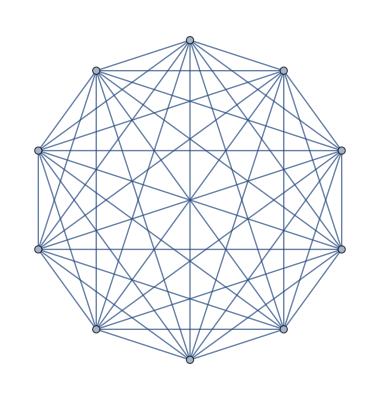

{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,1<->8,1<->9,1<->10,2<->3,2<->4,2<->5,2<->6,2<->7,2<->8,2<->9,2<->10,3<->4,3<->5,3<->6,3<->7,3<->8,3<->9,3<->10,4<->5,4<->6,4<->7,4<->8,4<->9,4<->10,5<->6,5<->7,5<->8,5<->9,5<->10,6<->7,6<->8,6<->9,6<->10,7<->8,7<->9,7<->10,8<->9,8<->10,9<->10}

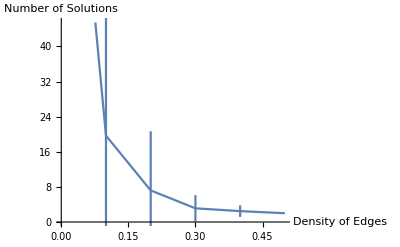

```mathematica
G=DGRandomMDGP[10]["G"]
nSample=25;
density={0,0.1,0.2,0.3,0.4,0.5}; (* density of edges *)
(* generating sample data *)
Needs["ErrorBarPlots`"]
allEdges=EdgeList[G]
nSols=Table[0,{i,Length[density]},{j,nSample}];
g=Table[0,{i,Length[density]},{j,nSample}];
For[i=1,i≤Length[density],i++,
d=density[[i]];
For[j=1,j≤nSample,j++,
(* create subgraph *)
gij=G;
For[k=1,k≤Length[allEdges],k++,
ek=allEdges[[k]];
If[RandomReal[]>d&&Abs[ek[[1]]-ek[[2]]]>3,gij=EdgeDelete[gij,ek]]
];
g[[i]][[j]]=gij;
(* solve instance *)
nodes=Table[i,{i,Length[VertexList[gij]]}];
{S,work}=DGBPSolver[gij,nodes];
nSols[[i]][[j]]=Length[S["Points"]];
];
];
(* plot results *)
ErrorListPlot[Table[{{density[[i]],Mean[nSols[[i]]]},ErrorBar[StandardDeviation[nSols[[i]]]]},{i,Length[density]}],
Joined->True,
AxesLabel->{"Density of Edges", "Number of Solutions"}]
```

### Exemplo 6 (Compara soluções visualmente):

```mathematica
(* gera uma instância MDGP com n átomos *)
n=10;
P=DGRandomMDGP[n,0.0,5];
(* define uma ordem - a ordem natural *)
nodes=DGNaturalOrdering[P["G"]];
(* tenta resolver a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em [s]) usado nesta tarefa *)
timeElapsed=Timing[{S,work}=DGBPSolver[P["G"],nodes,False,True]][[1]];
Print["TimeElapsed = ",Style[timeElapsed,Red]];
Print["\n"];
(* calcula o erro da primeira solução *)
DGRelativeResidue[P["G"],S["Points"][[1]],True];
Print["\n"];
X=S["Points"];
(* Extrai de S a lista dos caminhos B correspondentes a cada solução do problema *)
B=S["Branches"];
(* exibe soluções, caminhos que levaram as soluções e informações sobre a árvore do BP *)
Print["\n"];
Print["UnderBar[Soluções]"];
Print[Style[MatrixForm[X],Red]];
Print["\n"];
Print["UnderBar[Caminhos das soluções]"];
Print[Style[B,Red]];
Print["\n"];
```

DGBPSolver

Number of solutions: 2

TimeElapsed = 0.03125

Solution Quality

Number of nodes      : 10

Number of edges      : 35

Relative error bounds: {0.,4.62714×10^-14}

Mean relative error  : 1.96908×10^-15

UnderBar[Soluções]

((0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55066
1.44226
-0.16633) | (-3.91481
0.82944
-1.5156) | (-3.57535
-0.658292
-1.50577) | (-3.96113
-1.27599
-2.84678) | (-3.30503
-0.487428
-3.97655) | (-3.73774
-1.06882
-5.31947) | (-5.22337
-0.79557
-5.53605)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55066
1.44226
0.16633) | (-3.91481
0.82944
1.5156) | (-3.57535
-0.658292
1.50577) | (-3.96113
-1.27599
2.84678) | (-3.30503
-0.487428
3.97655) | (-3.73774
-1.06882
5.31947) | (-5.22337
-0.79557
5.53605))

UnderBar[Caminhos das soluções]

{{1,1,1,0,0,0,1,1,0,1},{1,1,1,1,1,1,0,0,1,0}}

```mathematica
(* plota as soluções X *)
graf = DGPlot3DBackbone[X,.2,.08];
graf1 = DGPlot3DBackbone[X[[1,;;]],.2,.08];
graf2 = DGPlot3DBackbone[X[[2,;;]],.2,.08];
Grid[Table[{graf1,graf2, graf},1]]
(*graf3 = DGPlot3DBackbone[X[[3,;;]],.2,.08];
graf4 = DGPlot3DBackbone[X[[4,;;]],.2,.08];
Grid[Table[{graf1,graf2,graf3,graf4, graf},1]]*)
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

### Exemplo 7 (Testes com n ≥ 10):

```mathematica
(* gera uma instância MDGP com n átomos *)
n=50;
P=DGRandomMDGP[n,0.0,5];
(* define uma ordem - a ordem natural *)
nodes=DGNaturalOrdering[P["G"]];
(* tenta resolver a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em [s]) usado nesta tarefa *)
timeElapsed=Timing[{S,work}=DGBPSolver[P["G"],nodes,False,True]][[1]];
Print["TimeElapsed = ",Style[timeElapsed,Red]];
Print["\n"];
(* calcula o erro da primeira solução *)
DGRelativeResidue[P["G"],S["Points"][[1]],True];
Print["\n"];
```

DGBPSolver

Number of solutions: 2

TimeElapsed = 0.265625

Solution Quality

Number of nodes      : 50

Number of edges      : 400

Relative error bounds: {0.,3.2465×10^-10}

Mean relative error  : 2.18098×10^-11

```mathematica
(* plota as soluções X *)
graf = DGPlot3DBackbone[X,.2,.08];
graf1 = DGPlot3DBackbone[X[[1,;;]],.2,.08];
graf2 = DGPlot3DBackbone[X[[2,;;]],.2,.08];
Grid[Table[{graf1,graf2, graf},1]]
(*graf3 = DGPlot3DBackbone[X[[3,;;]],.2,.08];
graf4 = DGPlot3DBackbone[X[[4,;;]],.2,.08];
Grid[Table[{graf1,graf2,graf3,graf4, graf},1]]*)
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

### Exemplo 8 (Encontra solução e exibe caminho na árvore, para n = 9):

```mathematica
(* gera uma instância MDGP com n átomos *)
n=9;
P=DGRandomMDGP[n, 0.0, 4];
(* define uma ordem - a ordem natural *)
nodes=DGNaturalOrdering[P["G"]];
(* tenta resolver a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em [s]) usado nesta tarefa *)
timeElapsed=Timing[{S,work}=DGBPSolver[P["G"],nodes,False,True]][[1]];
Print["TimeElapsed = ",Style[timeElapsed,Red]];
Print["\n"];
(* calcula o erro da primeira solução *)
DGRelativeResidue[P["G"],S["Points"][[1]],True];
Print["\n"];
X=S["Points"];
(* Extrai de S a lista dos caminhos B correspondentes a cada solução do problema *)
B=S["Branches"];
(* exibe soluções, caminhos que levaram as soluções e informações sobre a árvore do BP *)
Print["\n"];
Print["UnderBar[Soluções]"];
Print[Style[MatrixForm[X],Red]];
Print["\n"];
Print["UnderBar[Caminhos das soluções]"];
Print[Style[B,Red]];
Print["\n"];
```

DGBPSolver

Number of solutions: 4

TimeElapsed = 0.078125

Solution Quality

Number of nodes      : 9

Number of edges      : 26

Relative error bounds: {0.,2.75009×10^-14}

Mean relative error  : 2.15575×10^-15

UnderBar[Soluções]

((0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-1.48179
2.17224
-1.2192) | (-2.07395
3.57744
-1.27777) | (-3.57841
3.50507
-1.03273) | (-3.84164
2.84813
0.319237) | (-3.15388
3.65374
1.41772) | (-3.744
5.06035
1.46096)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-1.48179
2.17224
-1.2192) | (-1.90124
3.63838
-1.16292) | (-1.66044
4.18181
0.242559) | (-2.43933
3.34292
1.25165) | (-3.92493
3.38168
0.905033) | (-4.43201
4.8176
1.0035)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-1.48179
2.17224
1.2192) | (-1.90124
3.63838
1.16292) | (-1.66044
4.18181
-0.242559) | (-2.43933
3.34292
-1.25165) | (-3.92493
3.38168
-0.905033) | (-4.43201
4.8176
-1.0035)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-1.48179
2.17224
1.2192) | (-2.07395
3.57744
1.27777) | (-3.57841
3.50507
1.03273) | (-3.84164
2.84813
-0.319237) | (-3.15388
3.65374
-1.41772) | (-3.744
5.06035
-1.46096))

UnderBar[Caminhos das soluções]

{{1,1,1,0,0,1,0,0,0},{1,1,1,0,1,0,1,1,1},{1,1,1,1,0,1,0,0,0},{1,1,1,1,1,0,1,1,1}}

```mathematica
Print["UnderBar[Caminhos das soluções]"];
Print[Style[B,Red]];
Print["\n"];
```

UnderBar[Caminhos das soluções]

{{1,1,1,0,0,1,0,0,0},{1,1,1,0,1,0,1,1,1},{1,1,1,1,0,1,0,0,0},{1,1,1,1,1,0,1,1,1}}

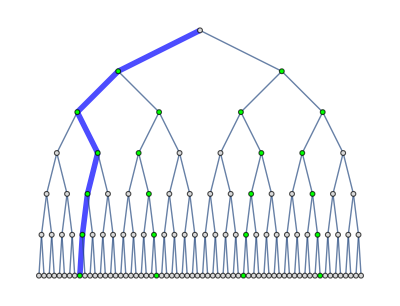

```mathematica
(* Exibe na árvore BP o caminho de uma solução encontrada; 
   obs1: começa no 3^(o̲) nível
obs2: DGByHandTreeFromBranches[G_, branch_, branches_, check_]:=Module[...]
 obs3: no mdgp.nb: >> DGByHandTreeFromBranches[G, {ω4,ω5,ω6,ω7,ω8,ω9}, branches, BP]
*)
plot1 = DGByHandTreeFromBranches[P["G"],B[[1,4;;]],B[[;;,4;;]],True]
```

```mathematica
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
plot2 = DGPrintGraph[G];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8368 | 3.8368 | 3.8368
4 | 1 | 5 | 4.36853 | 4.36853 | 4.36853
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.94229 | 2.94229 | 2.94229
8 | 2 | 7 | 5.26087 | 5.26087 | 5.26087
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 3.83404 | 3.83404 | 3.83404
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 4 | 7 | 3.02839 | 3.02839 | 3.02839
15 | 5 | 6 | 1.526 | 1.526 | 1.526
16 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
17 | 5 | 8 | 3.08624 | 3.08624 | 3.08624
18 | 6 | 7 | 1.526 | 1.526 | 1.526
19 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
20 | 6 | 9 | 2.92974 | 2.92974 | 2.92974
21 | 7 | 8 | 1.526 | 1.526 | 1.526
22 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
23 | 8 | 9 | 1.526 | 1.526 | 1.526

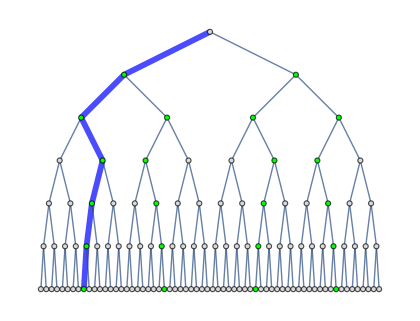
-Graphics- |  | i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8368 | 3.8368 | 3.8368
4 | 1 | 5 | 4.36853 | 4.36853 | 4.36853
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.94229 | 2.94229 | 2.94229
8 | 2 | 7 | 5.26087 | 5.26087 | 5.26087
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 3.83404 | 3.83404 | 3.83404
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 4 | 7 | 3.02839 | 3.02839 | 3.02839
15 | 5 | 6 | 1.526 | 1.526 | 1.526
16 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
17 | 5 | 8 | 3.08624 | 3.08624 | 3.08624
18 | 6 | 7 | 1.526 | 1.526 | 1.526
19 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
20 | 6 | 9 | 2.92974 | 2.92974 | 2.92974
21 | 7 | 8 | 1.526 | 1.526 | 1.526
22 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
23 | 8 | 9 | 1.526 | 1.526 | 1.526

Null

```mathematica
(* plota uma solução na árvore BP e os dados de entrada *)
Grid[Table[{plot1,plot2},1]]
```

### Exemplo 9 (Encontra solução e exibe caminho na árvore, para n = 11):

```mathematica
(* gera uma instância MDGP com n átomos *)
n=11;
P=DGRandomMDGP[n,0.0,5];
(* define uma ordem - a ordem natural *)
nodes=DGNaturalOrdering[P["G"]];
(* tenta resolver a instância com o algoritmo BP (DGBPSolver[]) e calcula o tempo (em [s]) usado nesta tarefa *)
timeElapsed=Timing[{S,work}=DGBPSolver[P["G"],nodes,False,True]][[1]];
Print["TimeElapsed = ",Style[timeElapsed,Red]];
Print["\n"];
(* calcula o erro da primeira solução *)
DGRelativeResidue[P["G"],S["Points"][[1]],True];
Print["\n"];
X=S["Points"];
(* Extrai de S a lista dos caminhos B correspondentes a cada solução do problema *)
B=S["Branches"];
(* exibe soluções, caminhos que levaram as soluções e informações sobre a árvore do BP *)
Print["\n"];
Print["UnderBar[Soluções]"];
Print[Style[MatrixForm[X],Red]];
Print["\n"];
Print["UnderBar[Caminhos das soluções]"];
Print[Style[B,Red]];
Print["\n"];
```

DGBPSolver

Number of solutions: 2

TimeElapsed = 0.046875

Solution Quality

Number of nodes      : 11

Number of edges      : 43

Relative error bounds: {0.,1.10586×10^-14}

Mean relative error  : 1.28294×10^-15

UnderBar[Soluções]

((0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55599
1.44038
-0.107066) | (-4.06186
2.87984
-0.133926) | (-3.91329
3.49623
1.25412) | (-2.44492
3.46631
1.66845) | (-1.6108
4.22058
0.636954) | (-2.1155
5.65655
0.52769) | (-2.03608
6.32814
1.89565) | (-2.69728
7.7017
1.82612)
(0
0
0) | (-1.526
0
0) | (-2.03376
1.43905
0) | (-3.55599
1.44038
0.107066) | (-4.06186
2.87984
0.133926) | (-3.91329
3.49623
-1.25412) | (-2.44492
3.46631
-1.66845) | (-1.6108
4.22058
-0.636954) | (-2.1155
5.65655
-0.52769) | (-2.03608
6.32814
-1.89565) | (-2.69728
7.7017
-1.82612))

UnderBar[Caminhos das soluções]

{{1,1,1,0,0,0,1,1,1,0,0},{1,1,1,1,1,1,0,0,0,1,1}}

```mathematica
Print["n = ",Style[n,Red]];
Print["UnderBar[Caminhos das soluções]"];
Print[Style[B,Red]];
Print["\n"];
```

n = 11

UnderBar[Caminhos das soluções]

{{1,1,1,0,0,0,1,1,1,0,0},{1,1,1,1,1,1,0,0,0,1,1}}

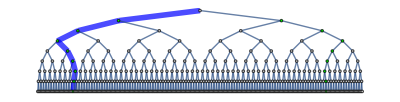

```mathematica
(* Exibe uma solução encontrada na árvore BP; 
    obs1: começa no 3^(o̲) nível
obs2: DGByHandTreeFromBranches[G_, branch_, branches_, check_]:=Module[...]
 obs3: no mdgp.nb: >> DGByHandTreeFromBranches[G, {ω4,ω5,ω6,ω7,ω8,ω9}, branches, BP]
*)
plot1 = DGByHandTreeFromBranches[P["G"],B[[1,4;;]],B[[;;,4;;]],True]
```

```mathematica
(* exibe o grafo associado a instância G = (V, E, d) em forma de tabela *)
Print["UnderBar[G  =  (V,  E,  d)]"];
plot2 = DGPrintGraph[G];
Print["\n"];
```

UnderBar[G  =  (V,  E,  d)]

| i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8368 | 3.8368 | 3.8368
4 | 1 | 5 | 4.36853 | 4.36853 | 4.36853
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.94229 | 2.94229 | 2.94229
8 | 2 | 7 | 5.26087 | 5.26087 | 5.26087
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 3.83404 | 3.83404 | 3.83404
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 4 | 7 | 3.02839 | 3.02839 | 3.02839
15 | 5 | 6 | 1.526 | 1.526 | 1.526
16 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
17 | 5 | 8 | 3.08624 | 3.08624 | 3.08624
18 | 6 | 7 | 1.526 | 1.526 | 1.526
19 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
20 | 6 | 9 | 2.92974 | 2.92974 | 2.92974
21 | 7 | 8 | 1.526 | 1.526 | 1.526
22 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
23 | 8 | 9 | 1.526 | 1.526 | 1.526

```mathematica
(* plota uma solução na árvore BP e os dados de entrada *)
Grid[Table[{plot1,plot2},1]]
```

-Graphics- |  | i | j | dij | lij | uij
1 | 1 | 2 | 1.526 | 1.526 | 1.526
2 | 1 | 3 | 2.49139 | 2.49139 | 2.49139
3 | 1 | 4 | 3.8368 | 3.8368 | 3.8368
4 | 1 | 5 | 4.36853 | 4.36853 | 4.36853
5 | 2 | 3 | 1.526 | 1.526 | 1.526
6 | 2 | 4 | 2.49139 | 2.49139 | 2.49139
7 | 2 | 5 | 2.94229 | 2.94229 | 2.94229
8 | 2 | 7 | 5.26087 | 5.26087 | 5.26087
9 | 3 | 4 | 1.526 | 1.526 | 1.526
10 | 3 | 5 | 2.49139 | 2.49139 | 2.49139
11 | 3 | 6 | 3.83404 | 3.83404 | 3.83404
12 | 4 | 5 | 1.526 | 1.526 | 1.526
13 | 4 | 6 | 2.49139 | 2.49139 | 2.49139
14 | 4 | 7 | 3.02839 | 3.02839 | 3.02839
15 | 5 | 6 | 1.526 | 1.526 | 1.526
16 | 5 | 7 | 2.49139 | 2.49139 | 2.49139
17 | 5 | 8 | 3.08624 | 3.08624 | 3.08624
18 | 6 | 7 | 1.526 | 1.526 | 1.526
19 | 6 | 8 | 2.49139 | 2.49139 | 2.49139
20 | 6 | 9 | 2.92974 | 2.92974 | 2.92974
21 | 7 | 8 | 1.526 | 1.526 | 1.526
22 | 7 | 9 | 2.49139 | 2.49139 | 2.49139
23 | 8 | 9 | 1.526 | 1.526 | 1.526

### Exemplo 10 (Exercício):

No Exemplo 8 se diminuirmos o valor de corte r_c = 4 para r_c = 3 (i.e., alterarmos P=DGRandomMDGP[n, 0.0, 4] 
para P=DGRandomMDGP[n, 0.0, 3]) é esperado que o número de soluções deva aumentar ou diminuir? E se aumentarmos 
o valor de corte para r_c = 6, o número de soluções aumenta ou diminui? Tente usar o Mathematica para verificar a resposta 
correta.